```mathematica
$RecursionLimit=10000
```

10000

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
zetaHurwitz[n_,s_,y_,0]:=UnitStep[n-1]
zetaHurwitz[n_,s_,y_,1]:=zetaHurwitz[n,s,y,1]=HarmonicNumber[Floor[n],s]-HarmonicNumber[y,s]
zetaHurwitz[n_,s_,y_,2]:=zetaHurwitz[n,s,y,2]=Sum[(m^(-2s))+2(m^-s) (zetaHurwitz[Floor[n/m],s,m,1]),{m,y+1,Floor[n^(1/2)]}]
zetaHurwitz[n_,s_,y_,k_]:=zetaHurwitz[n,s,y,k]=Sum[(m^(-s k))+k(m^(-s(k-1))) zetaHurwitz[Floor[n/(m^(k-1))],s,m,1]+Sum[binomial[k,j] (m^-s)^j zetaHurwitz[Floor[n/(m^j)],s,m,k-j],{j,1,k-2}],{m,y+1,Floor[n^(1/k)]}]
zeta[n_,s_,z_]:=Expand@Sum[binomial[z,k]zetaHurwitz[n,s,1,k],{k,0,Log2@n}]
zetaAlt[n_,s_,x_,z_]:=Expand@Sum[(-1)^j binomial[z,j] x^(j(1-s))zeta[n/(x^j),s,z],{j,0,Log[x,n]}]
zetaMinus1Scaled[n_,s_,y_,k_]:=y^(k(1-s)) zetaHurwitz[n y^-k,s,y^-1,k]
zetaScaled[n_,s_,y_,z_]:=Expand@Sum[binomial[z,k]zetaMinus1Scaled[n,s,y,k],{k,0,Log[y+1,n]}]
```

```mathematica
Po[n_,s_,x_]:=Sum[x^(k(1-s))/k,{k,1,Floor@Log[x,n]}]-Sum[x^(k(1-s))/k,{k,1,Floor@Log[x,1.4513692348833810502839684858]}]
```

```mathematica
Po[100.,-1.5,1.00001]
```

9628.14

```mathematica
LogIntegral[100.^2.5]
```

9629.81

```mathematica
Log[1.00001,1.4513692348833810502839684858]
```

37250.9

```mathematica
Log[1.00001,1.45136]
```

37250.3

```mathematica
Clear[dz,Dz,Ez]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Expand@Product[(-1)^p[[2]] binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_]:=Dz[n,z]=Expand@Sum[dz[j,z],{j,1,n}]

Ez[n_,z_,x_]:=Expand@Sum[(-1)^j binomial[z,j] x^j Dz[n/(x^j),z],{j,0,Log[x,n]}]
E2[n_,k_,x_]:=Sum[(-1)^(k-j)binomial[k,j]Ez[n,j,x],{j,0,k}]
E2z[n_,z_,x_]:=Sin[Pi z]/Pi Sum[(-1)^k/(z-k) E2[n,k,x],{k,0,If[x<2,Log[x,n],Log[2,n]]}]
z2a[n_,x_]:=(D[Ez[n,z,x],z]/.z->0)+Sum[x^k/k,{k,1,Log[x,1.4513692348833810502839684858]}]
```

```mathematica
z2[n_,x_]:=(D[zetaAlt[n,0,x,z],z]/.z->0)+Sum[x^k/k,{k,1,Log[x,1.4513692348833810502839684858]}]
```

```mathematica
z2[100,1.01]
```

-1.52211

```mathematica
Sum[PrimePi[100^(1/k)]/k,{k,1,Log2@100}]-LogIntegral[100.]
```

-1.59281

```mathematica
z2[100,1.005]
```

-1.61434

```mathematica
z2a[100,1.005]
```

$Aborted

```mathematica
Sum[PrimePi[6.^(1/k)]/k,{k,1,Log2@6.}]-LogIntegral[6.]
```

-0.722222

```mathematica
z2[6.,1.005]
```

-0.730088

```mathematica
z2[6.,1.002]
```

-0.719911

```mathematica
Log[1.002,6]
```

896.775

```mathematica
Table[E2[100,k,2],{k,0,8}]
```

{1,-1,3,-4,-8,9,-5,0,0}

```mathematica
Limit[D[E2z[100,z,3/2],z],z->0]
```

-8149753/2365440

```mathematica
D[Ez[100,z,3/2],z]/.z->0
```

-8149753/2365440

```mathematica
Clear[ff]
ff[n_,s_,x_,y_,z_]:=If[n<x y, 1, Expand@Sum[binomial[z,k](x^(1-s) y^-s)^k ff[n/(x y)^k, s, x, 1+y, z-k],{k,0,Log[x y,n]}]]
f2[n_,s_,x_,z_]:=ff[n,s,x,1+1/x,z]
```

```mathematica
N@f2[100,-1,1/3,z]
```

1.+1193.42 z+2167.06 z^2+1216.08 z^3+373.387 z^4+59.4418 z^5+6.19276 z^6+0.3988 z^7+0.018873 z^8+0.000503346 z^9+0.0000125962 z^10+1.62017×10^-7 z^11+1.39947×10^-9 z^12+1.31732×10^-11 z^13+2.0211×10^-14 z^14+6.54708×10^-17 z^15+1.1078×10^-19 z^16

```mathematica
N@zetaScaled[10,0,1/2,z]
```

1.+5.10521 z+3.29167 z^2+0.566406 z^3+0.0364583 z^4+0.000260417 z^5

```mathematica
Clear[gg]
gg[n_,s_,x_,j_,z_]:=If[n<j, 1, Expand@Sum[binomial[z,k]x^-k j^(-s k) gg[n/j^k, s, x, j+1/x, z-k],{k,0,Log[j,n]}]]
g2[n_,s_,x_,z_]:=gg[n,s,x,1+1/x,z]
```

```mathematica
N@g2[10,0,2,z]
```

1.+5.10521 z+3.29167 z^2+0.566406 z^3+0.0364583 z^4+0.000260417 z^5

```mathematica
Clear[hh]
t[n_,x_]:=(Floor[n]-Floor[n-1/x])-(x+1)/x (Floor[n x /(x+1)]-Floor[(n x-1)/(x+1)])
pw[n_,k_]:=If[n==0&&k==0,1,n^k]
hh[n_,s_,x_,j_,z_]:=If[n<j, 1, Expand@Sum[ binomial[z,k]pw[t[j,x],k]j^(-s k) hh[n/j^k, s, x, j+1/x, z-k],{k,0,Log[j,n]}]]
h2[n_,s_,x_,z_]:=hh[n,s,x,1+1/x,z]
```

```mathematica
h2[10,0,3,z]
```

1-(589516 z)/229635+(1500281 z^2)/459270-(1052917 z^3)/590490+(341204 z^4)/295245-(141968 z^5)/295245+(24704 z^6)/295245-(17408 z^7)/2066715+(512 z^8)/2066715

```mathematica
zetaAlt[10,0,4/3,z]
```

1-(589516 z)/229635+(1500281 z^2)/459270-(1052917 z^3)/590490+(341204 z^4)/295245-(141968 z^5)/295245+(24704 z^6)/295245-(17408 z^7)/2066715+(512 z^8)/2066715

```mathematica
Clear[ee,ef]
ef[n_,j_,z_]:=ef[n,j,z]=Expand@If[n<j,1,Sum[binomial[z,k](-1)^((j+1)k) ef[n/j^k, j+1, z-k],{k,0,Log[j,n]}]]
ee[n_,j_,z_]:=ee[n,j,z]=Expand@If[n<j,1,Table[binomial[z,k](-1)^((j+1)k) ef[n/j^k, j+1, z-k],{k,0,Log[j,n]}]]
```

```mathematica
D[ee[100,2,z],z]/.z->0
```

{-9/4,2,-1,5/3,-1/4,4/5,-1/6}

```mathematica
pl[n_]:=Sum[PrimePi[n^(1/k)]/k,{k,1,Log2@n}]-Sum[2^k/k,{k,1,Log2@n}]
pl2[n_]:=Sum[PrimePi[n^(1/k)]/k,{k,1,Log2@n}]
pl3[n_]:=Sum[PrimePi[n^(1/k)]/k,{k,1,Log2@n}]-LogIntegral[n]
```

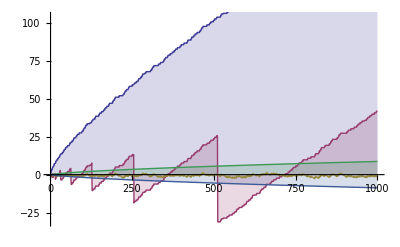

```mathematica
DiscretePlot[{pl2[n],pl[n], pl3[n],1/(8 Pi) Log[n] n^(1/2), -1/(8 Pi) Log[n] n^(1/2)},{n,1,1000}]
```

```mathematica
N@pl2[100]
```

28.5333